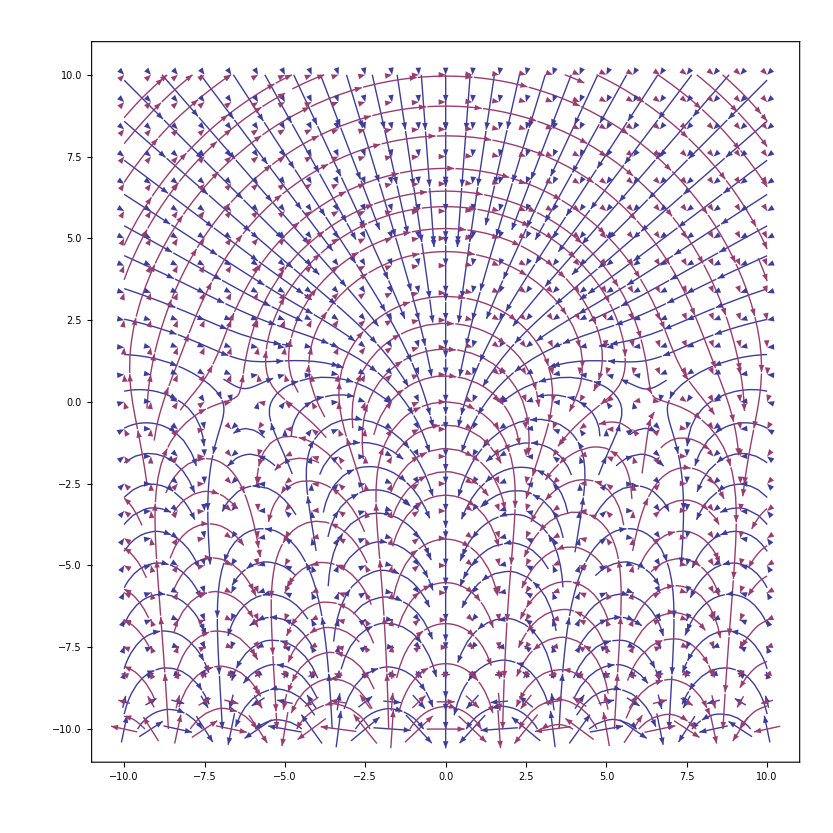

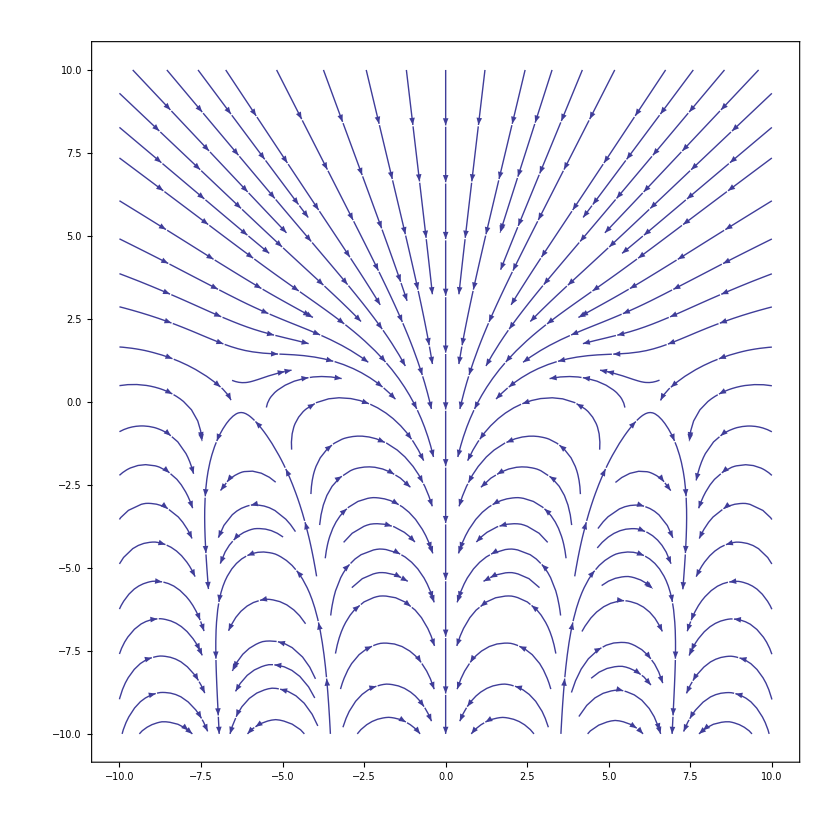

```mathematica
L= 10;
z = x+ I y;
ϕx=Re[(Exp[I * z]-1)/z];
ψy=ϕx;
ψx=Im[(Exp[I * z]-1)/z];
ϕy=-ψx;
StreamPlot[{{ϕx,ϕy},{ψx,ψy}},{x,-L,L},{y,-L,L},PerformanceGoal-> "Quality",VectorPoints-> Fine]
StreamPlot[{{ϕx,ϕy}},{x,-L,L},{y,-L,L},PerformanceGoal-> "Quality",VectorPoints-> None]
```

```mathematica
ComplexExpand[ψx]
ComplexExpand[ψy]
```

y/(x^2+y^2)-(ⅇ^-y y Cos[x])/(x^2+y^2)+(ⅇ^-y x Sin[x])/(x^2+y^2)

-x/(x^2+y^2)+(ⅇ^-y x Cos[x])/(x^2+y^2)+(ⅇ^-y y Sin[x])/(x^2+y^2)

```mathematica
A=Sqrt[1+4 π^2]/(8 π^2)
```

(√(1+4 π^2))/(8 π^2)

```mathematica
N[A]
```

0.080579

```mathematica
Sqrt[c/N[4*A]]
```

0.698318

```mathematica
c =N[Cos[ArcTan[2π]]]
```

0.157177

```mathematica
β=100;
h[t_]:=NIntegrate[(Exp[I u]-1)/u,{u,0,t}]
phi[t_]:=Exp[β*h[t]]
```

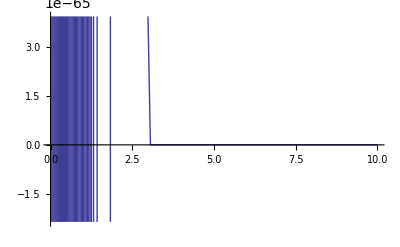

```mathematica
Plot[Re[phi[t]],{t,0,10}]
A=Table[phi[t],{t,0,100,0.1}];
```

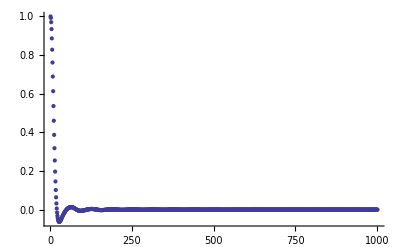

```mathematica
ListPlot[A]
```

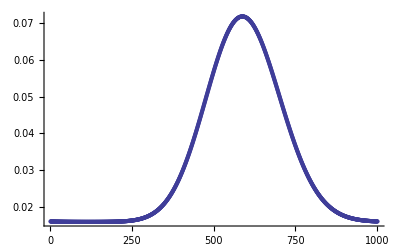

```mathematica
ListPlot[Re[InverseFourier[A]]]
```

```mathematica
Needs["FourierSeries`"]
```

NInverseFourierTransform::shdw: Symbol NInverseFourierTransform appears in multiple contexts FourierSeries`Global`; definitions in context FourierSeries` may shadow or be shadowed by other definitions.

```mathematica
NInverseFourierTransform[phi[t],t,x]
```

NIntegrate::nlim: u = t is not a valid limit of integration.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NInverseFourierTransform[ⅇ^NIntegrate[(Exp[ⅈ u]-1)/u,{u,0,t}],t,x]

```mathematica
FFT
```

```mathematica
a = 10;
b = 100;

f[x_]:=If[x<a,0,If[x>b,0,x^(-1)]]
```

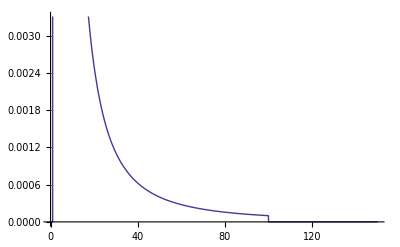

```mathematica
Plot[f[x],{x,0,150}]
```

```mathematica
phi= FourierTransform[f[x],x,t]
```

1/(√(2 π))(-CosIntegral[10 t]+CosIntegral[100 t]-ⅈ (SinIntegral[10 t]-SinIntegral[100 t]))

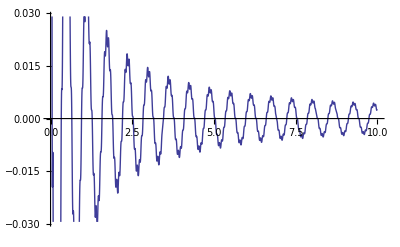

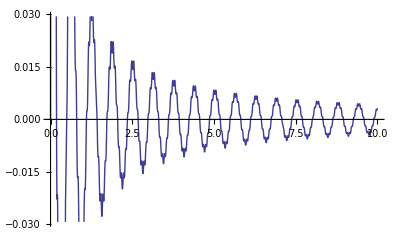

```mathematica
Plot[Re[phi],{t,0,10}]
Plot[Im[phi],{t,0,10}]
```

```mathematica
Limit[CosIntegral[c ],c-> ∞]
```

0

```mathematica
ExpIntegral￿
```

```mathematica
f[t_]:=
```